## Scoping Constructs

## Learning Objectives

### Scoping Constructs

Automatic scoping of name

Automatic scoping of values

Attributes for automatic scoping

Module: localizing names

With: localizing constants

Block: localizing values

## Constructs That Provide Automatic Scoping

The flexibility of Wolfram Language's symbolic architecture is reflected in its rich collection of carefully defined constructs for localization and modularization. Multiple forms of scoping allow for more elegant, readable and efficient programs.

### Automatic Name Scoping

The Wolfram Language function Function makes it possible to create a pure function with automatically scoped formal variables. (The shorthand form of Function uses Slot (#), which obviates the need for variable scoping at all.)

RuleDelayed (:>) and SetDelayed (:=) make it possible to use named pattern variables that are automatically scoped.

### Automatic Value Scoping

Iterator variables are automatically scoped in functions like Table:

```mathematica
i="Hello";{Table[i+1,{i,5}],i}
```

The scoping within the Table expression is indicated by the color of the iterator i.

Some other functions that provide automatic scoping are Do, Sum, Plot, Plot3D and NDSolve. You will notice the same coloring in automatically scoped variables used within these functions.

### Attributes for Automatic Scoping

Various built-in functions heavily rely on Hold* attributes for effective evaluation.

#### SetDelayed without its HoldAll attribute works like Set

Use delayed assignment for f:

```mathematica
ClearAll[f];
x=10;
f:=x^2
```

SetDelayed behaves as expected:

```mathematica
x=2;
f
x=3;
f
```

4

9

Check the attributes of SetDelayed:

```mathematica
Attributes[SetDelayed]
```

{HoldAll,Protected,SequenceHold}

```mathematica
ClearAttributes[SetDelayed,HoldAll];
SetAttributes[SetDelayed,HoldFirst];
```

```mathematica
ClearAll[f];
x=10;
f:=x^2
```

Without the HoldAll attribute, SetDelayed evaluates the right-hand side with the pre-set value of x:

```mathematica
x=2;
f
x=3;
f
```

100

100

#### Plot needs the HoldAll attribute to keep the function from evaluating

Check the attributes of Plot:

```mathematica
Attributes[Plot]
```

{HoldAll,Protected,ReadProtected}

Plot is able to localize the variables in its first argument using the HoldAll attribute:

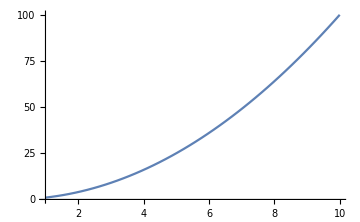

```mathematica
i=2;
Plot[i^2,{i,1,10}]
```

The first argument gets evaluated when you remove the HoldAll attribute:

```mathematica
ClearAttributes[Plot,HoldAll];
SetAttributes[Plot,HoldRest];
```

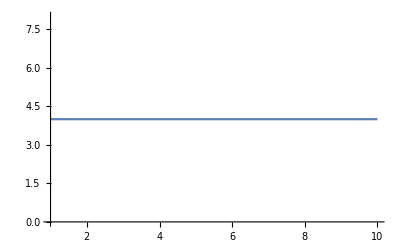

```mathematica
Plot[i^2,{i,1,10}]
```

```mathematica
ClearAttributes[Plot,HoldRest];
SetAttributes[Plot,HoldAll];
```

#### Table needs the HoldAll attribute to use the iterator

Check the attributes of Table:

```mathematica
Attributes[Table]
```

{HoldAll,Protected}

The iterator in the second argument is not evaluated and thus can be scoped:

```mathematica
i=2;
Table[i^2,{i,1,5}]
```

{1,4,9,16,25}

If you allow the evaluation of the first argument:

```mathematica
ClearAttributes[Table,HoldAll];
SetAttributes[Table,HoldRest];
```

```mathematica
Table[i^2,{i,1,5}]
```

{4,4,4,4,4}

If you allow the evaluation of the second argument with the iterator:

```mathematica
ClearAttributes[Table,HoldRest]
SetAttributes[Table,HoldFirst];
```

```mathematica
Table[i^2,{i,1,5}]
```

Table::itraw: Raw object 2 cannot be used as an iterator.

Table[i^2,{2,1,5}]

## The Need for Local Variables

The default scope for symbols is global. Every time you use a name like x, Wolfram Language normally assumes that you are referring to the same object.

Sometimes you want to use the name x to refer to two quite different variables in two different pieces of code. In this case, you need the x in each program to be treated as a local variable.

### Module: Localizing Names

Module uses what is known as lexical scoping. This means the name of the symbol is localized to keep it from clashing with any other variable of the same name in the global context. This is done by changing the name to have a unique value inside the Module.

Define two variables in the global context. Specify two variables of the same name to also be local to a module:

```mathematica
{r,s}={100,200};
```

```mathematica
Module[{r,s},Print[{r,s}];{r,s}={1,2};{r,s}]
```

The global definitions have not changed:

```mathematica
{r,s}
```

Evaluating the module multiple times reveals that the names for r and s are changed each time the Module is evaluated, avoiding the problem of an incorrect value getting into the calculations. Symbols used in a Module are deleted when the module calculations are complete.

A typical use of Module would be in defining a function.

Here is an example of a function to find the greatest common divisor (GCD) of two integers using the Euclidean algorithm, which uses the local variables m and n:

```mathematica
gcd[m0_,n0_]:=
Module[{m=m0,n=n0},
While[n≠0,{m,n}={n,Mod[m,n]}];
m
]
```

```mathematica
gcd[270,192]
```

Note that m and n have no values in the "Global`" context:

```mathematica
{m,n}
```

## The Need for Local Constants

### With: Localizing Constants

If all that is needed is local constants, i.e. variables whose values never change within the body of the local code, it is better to use With, another lexical scoping construct. Values are assigned to the local constants as they are declared in the list that immediately follows the function head.

Define a global value for c:

```mathematica
c=42;
```

In a simple function, redefine c to hold a constant value only for the scope of the function:

```mathematica
e[m_]:=With[{c=Quantity[299792458, ("Meters")/("Seconds")]},m c^2]
```

```mathematica
e[1]
```

89875517873681764 m^2/s^2

```mathematica
?c
```

With can be thought of as a generalization of the ReplaceAll ( /. ) operator. It takes every occurrence of the symbol c in the body and replaces it with the value 299792458 "m""/""s".

With does not generate any new symbols. It does all the replacements before the body evaluates, and by that time no "constant symbols" are present; all of them have been replaced explicitly with their values.

## The Need for Local Values of Global Names

### Block: Localizing Values

Block uses a different method of scoping called dynamic scoping. In dynamic scoping, an entirely new symbol with a new name is not created. Only the value of the global symbol is localized and temporarily changed, and once the localizing body of code is executed, the global value is restored. So you could say that its effects are a little less local than those of lexical scoping constructs.

One example of using Block is to temporarily change the value of program variables like $RecursionLimit. This is typically used for temporarily resetting the value of the recursion limit, in case a deeply recursive computation gets you into trouble:

```mathematica
$RecursionLimit
```

```mathematica
Clear[a];Block[{$RecursionLimit=20},Do[a= a+1,{i,200}]]
```

Internally, Block is the mechanism that localizes iterators for built-in functions like Table, Do, Sum and Product.

### Test the Difference

```mathematica
$TimeZone
```

-5.

```mathematica
Now
```

Fri 1 Oct 2021 10:48:58GMT-5

```mathematica
Module[{$TimeZone},Print[$TimeZone];$TimeZone=3; Now]
```

$TimeZone$121540

Fri 1 Oct 2021 10:52:00GMT-5

```mathematica
With[{$TimeZone=3},Print[$TimeZone]; Now]
```

3

Thu 31 Oct 2024 19:42:01GMT-5

```mathematica
Block[{$TimeZone=3},Print[$TimeZone]; Now]
```

3

Fri 1 Nov 2024 03:42:04GMT+3

```mathematica
$TimeZone
```

-5.

#### Which one should you use?

If all you need is a local constant or a local value for a global variable, With or Block may be faster than Module:

```mathematica
Module[{x=2.},1/x]//RepeatedTiming
```

{1.795×10^-6,0.5}

```mathematica
Block[{x=2.},1/x]//RepeatedTiming
```

{6.41997×10^-7,0.5}

```mathematica
With[{x=2.},1/x]//RepeatedTiming
```

{7.82604×10^-7,0.5}

## References

Modules and Local Variables

Local Constants

Blocks and Local Values

Scoping Constructs